# Study When Different Turing Machines Compute the Same Function

## Introduction

In this essay, referring to the variables  and/or  out of context refers to the  states and/or  symbols of a Turing machine. We also say that setting a Turing machine to a nonnegative integer  refers to filling an interval  of the tape of length  for some  with the binary representation of  in big endian (natural left-to-right order). We ensure that  (i.e. the number of bits fits in ). Additionally, we say the value of a Turing machine is the number created by each cell on  as base- digits.

## Formalism

Let  be the set of all -state -color Turing machines. Each Turing machine in  represents a partial function  with input specified by the base  number formed by an interval  on the tape, where each color is an integer between 0 and . Define two Turing machines in  to be equivalent if they compute the same partial function on , or both do not exist. 
1. Determine the cardinality of .
2. For each distinct function (equivalence class), determine and analyze the range of worst-case running times.

## Theory

### The Halting Problem

### Rice’s Theorem

### Computational Complexity

## Optimization

Despite the undecidability of finding a universal way of reducing computation across Turing machines or even on one Turing machine, we can take inspiration from DFA (deterministic finite automaton) minimization. Specifically, one big optimization we can make is to declare that all Turing machines with rules that permute a dead state (unreachable from the initial state) to be equal: each of these permutations are unreachable anyway.

The diagram below shows two equivalent Turing machines, each with a different permutation of the rules from state 2, which is unreachable from state 1.

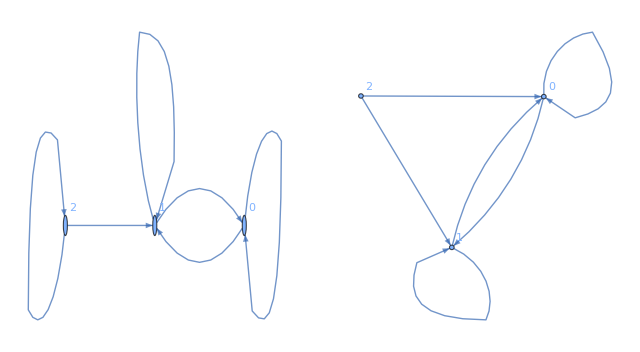

```mathematica
GraphicsRow[{
Graph[{1->1,1->0,0->1,0->0,2->1,2->2},VertexLabels->Automatic],
Graph[{1->1,1->0,0->1,0->0,2->0,2->1},VertexLabels->Automatic]
}]
```

Determining the reachable nodes is simply graph traversal. It is not hard to see that all state graphs have  vertices and  edges, resulting in a runtime of .

Additionally, notice that the numbering system of Turing machines in the Wolfram Language permutes rules in the following order: direction (-1 to 1), symbol (0 to ), and state (1 to ). For the rest of the essay, we will use this numbering without loss of generality. Notice that for consecutive unreachable states ending in state  (e.g. 2, 3 for ), their rule numbers will also be grouped separately so we only need to define the interval (start and end) of rule numbers of an equivalence class. For example, suppose for , state 3 is unreachable. Then there is a contiguous interval of rules, e.g. 0 to 20736, that are isomorphic. This allows us to skip ahead to the end of a block when we encounter its beginning. Consequently, this is also the only time we do not need to iterate, necessitating iteration through all Turing machines.

Since the goal of this first optimization step is to identify equivalent Turing machines only by analyzing rules, we can use a hash map from a constructed key to a count such that the key is equivalent for isomorphic rules. The key construction will be to replace unreachable states with 1’s. The following function gets this key and the state graph of a machine.

Set number of states and symbols:

```mathematica
states=3;
symbols=2;
```

getinfo requires the full form of a rule, but rule numbers are easier to comprehend, so we will use the following two resource functions to convert between them.

```mathematica
tmRuleFromNum=ResourceFunction["TuringMachineFromNumber"];
tmRuleToNum=ResourceFunction["TuringMachineToNumber"];
```

Get a rule’s hash map key and generate a state diagram from the rule:

```mathematica
getinfo[r_]:={
Transpose@{r[[All,1,2]],r[[All,2]]},
Graph[
r[[All,All,1]],
VertexLabels->Automatic
]
}
```

Transform a return value from getinfo into a true hash key that reduces all equivalent Turing machines to the same key.

```mathematica
ctransform=Compile[
{{reachable,_Integer,1},{key,_Integer,1}},
Flatten@
Table[
If[
MemberQ[reachable,j],
Flatten@key[[8*j-7;;8*j]],
Table[1,8]
],
{j,states}
],
CompilationTarget->"C",
RuntimeOptions->"Speed",
RuntimeAttributes->{Listable}
];
```

```mathematica
FunctionCompile
```

Given a list of full rules, it determines unreachable states from the graph, which it uses to construct the hash map key.

```mathematica
map=CreateDataStructure["HashTable"];
```

```mathematica
perm[d_Integer]:=(2*states*symbols)^(symbols*(states-d))
```

```mathematica
consQ[l:{___Integer}]:=First[l]==1&&Most[l]+1===Rest[l]
consQ[_List]:=False
```

```mathematica
prune[len_Integer]:=
Module[{rcur,tmp,cnt=CreateDataStructure["Counter",0]},
ResourceFunction["MonitorProgress"]@
Do[
If[
cnt["Get"]>0,
cnt["Decrement"],
With[{info=getinfo[tmRuleFromNum[i,states,symbols]]},
rcur=VertexOutComponent[info[[2]],1];
map[
"Insert",
(#->map["Lookup",#,0&]
+If[
consQ[rcur],
tmp=perm[Length[rcur]];cnt["Set",tmp-1];tmp,
1
]
)&@ctransform[rcur,Flatten@info[[1]]]
];
]
],
{i,0,len-1}
]
]
```

```mathematica
map=CreateDataStructure["HashTable"];
prune[84100];//AbsoluteTiming
map["Elements"]
```

{0.563339,Null}

{{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,2,0,-1,1,1,1,1,1,1,1,1}→144,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,3,0,-1,1,1,0,-1,0,1,0,1}→1,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,1,0,1,1,1,1,1,1,1,1,1}→144,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,3,0,-1,1,1,0,-1,0,1,1,-1}→1,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,1,0,-1,1,1,1,1,1,1,1,1}→144,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,1,1,-1,1,1,1,1,1,1,1,1}→144,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,1,1,1,1,1,1,1,1,1,1,1}→144,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,2,0,1,1,1,1,1,1,1,1,1}→144,{1,1,0,-1,0,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→20736,{1,1,0,-1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→20736,{1,1,0,-1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→20736,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,3,0,-1,1,1,0,-1,0,1,0,-1}→1,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,2,1,-1,1,1,1,1,1,1,1,1}→144,{1,1,0,-1,0,1,0,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→20736,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,3,0,-1,1,1,0,-1,0,1,1,1}→1,{1,1,0,-1,0,2,0,-1,1,1,0,-1,0,2,1,1,1,1,1,1,1,1,1,1}→144}

Prune the search space and place overlaps into a hash map:

```mathematica
map=CreateDataStructure["HashTable"];
prune[(2*states*symbols)^(states*symbols)];
```

```mathematica
elems=Import["./wsrp/project/main/mx/elems.mx"];
```

```mathematica
elems=map["Elements"];
Length@%
```

1775632

We can confirm that equivalence classes come in sizes of  for all nonnegative : for , we indeed have , , .

```mathematica
Select[elems,!MatchQ[#[[2]],1|144|20736]&]
```

{}

### Rule Extraction

Number of times each rule repeats:

```mathematica
ruleRepeats:=elems[[All,2]];
```

```mathematica
fullRules=With[
{
key=Transpose@{
Riffle[Range[states],Range[states]],
Table[BitAnd[i,1],{i,states*symbols}]
},
vals=Partition[#[[1]],3]&/@elems
},
ParallelMap[Table[key[[i]]->#[[i]],{i,states*symbols}]&,vals]
];
```

```mathematica
ruleNumsCompressed=ResourceFunction["MonitorProgress"]@Map[tmRuleToNum[#][[1]]&,fullRules];
fullRules=.
```

```mathematica
fullRules=Import["./wsrp/project/main/mx/full_rules.mx"];
```

```mathematica
ruleNumsCompressed=Import["./wsrp/project/main/mx/rule_nums_compressed.mx"];
```

## Search

```mathematica
dprad=8;
width=11;
bits=4;
```

```mathematica
stepTM[rule_Integer,stages_List,blockwidth_Integer]:=
With[
{tms=TuringMachine[{rule,3,2},stages[[-1]],blockwidth]},
Transpose@{
tms[[All,1]],
PadLeft[#[[2]],width,0,tms[[1,1,2]]-Length[#[[2]]]]&/@tms
}
]
```

```mathematica
trim=
Compile[
{{stages,_Integer,3},{width,_Integer}},
With[
{min=Min[stages[[All,1,2]],stages[[1,1,2]]-width]-1},
Transpose[{
stages[[All,1]],
ArrayPad[
stages[[All,2]],
{{0,0},{-min,stages[[1,1,2]]-Length[stages[[1,2]]]-stages[[1,1,3]]}}
]
}]
],
CompilationTarget->"C",
CompilationOptions->{"InlineExternalDefinitions" -> True},
RuntimeAttributes->{Listable}
];
```

```mathematica
htDP[rule_Integer,bits_Integer,blockwidth_Integer,maxdepth_Integer]:=
With[{dpG=CreateDataStructure["LeastRecentlyUsedCache",256]},
Table[
Module[
{
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",1],
cnt=CreateDataStructure["Counter",0],
tms,tmp,
flag=False,
cur={{0,0,0}}
},
(*Print[n];*)
(*Print["======"];*)
tms=NestWhile[
stepTM[rule,#,blockwidth]&,
stepTM[rule,{{{1,width,0},{IntegerDigits[n,2,width],0}}},blockwidth],
(
(*Print[#];*)
(*Print["------"];*)
i["Set",1];
While[
cur=#[[i["Get"]]];
Print[cur];
i["Get"]<=blockwidth&&!flag&&(*1-width<=*)cur[[1,3]]<=0,

(*Print[{i["Get"],cnt["Get"],cur}];*)
tmp=Join[
{cur[[1,1]],cur[[1,3]]},
PadLeft[cur[[2]],2*dprad-1,0,dprad+cur[[1,3]]-1]
];
(*Print[tmp];*)
If[
!(flag=dpG["KeyExistsQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpG["Insert",tmp->1],
dp["Insert",tmp->1]
]
];
(*Print[{i["Get"],flag,cur[[1,3]]}];*)
i["Increment"];
cnt["Increment"];
];
i["Get"]==blockwidth+1&&!flag&&(*1-width<=*)cur[[1,3]]<=0
)&,
1,maxdepth
];
Flatten[{
If[flag||cnt["Get"]==maxdepth*blockwidth,-1,cnt["Get"]],
If[tms[[i["Get"],1,3]]==1,FromDigits[tms[[i["Get"],2]],2],-1]
}]
],
{n,1,2^bits-1}
(*{n,2,2}*)
]
]
(* runs in #1 time and outputs #2 *)
htDP[ruleNumsCompressed[[50000]],4,4,16]
```

======

------

{{1,11,0},{0,0,0,0,0,0,0,0,0,0,1}}

{{3,10,-1},{0,0,0,0,0,0,0,0,0,0,1}}

{{1,9,-2},{0,0,0,0,0,0,0,0,0,0,1}}

{{3,10,-1},{0,0,0,0,0,0,0,0,0,0,1}}

{{1,9,-2},{0,0,0,0,0,0,0,0,0,0,1}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,0,0,1,0}}

{{3,12,1},{0,0,0,0,0,0,0,0,0,1,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,0,0,1,1}}

{{3,10,-1},{0,0,0,0,0,0,0,0,0,1,1}}

{{2,11,0},{0,0,0,0,0,0,0,0,0,1,1}}

{{3,12,1},{0,0,0,0,0,0,0,0,0,1,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,0,1,0,0}}

{{3,12,1},{0,0,0,0,0,0,0,0,1,0,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,0,1,0,1}}

{{3,10,-1},{0,0,0,0,0,0,0,0,1,0,1}}

{{1,9,-2},{0,0,0,0,0,0,0,0,1,0,1}}

{{3,8,-3},{0,0,0,0,0,0,0,0,1,0,1}}

{{1,7,-4},{0,0,0,0,0,0,0,0,1,0,1}}

------

{{1,7,-4},{0,0,0,0,0,0,0,0,0,0,0}}

{{3,8,-3},{0,0,0,0,0,0,0,0,0,0,0}}

{{1,7,-4},{0,0,0,0,0,0,0,0,0,0,0}}

{{3,8,-3},{0,0,0,0,0,0,0,0,0,0,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,0,1,1,0}}

{{3,12,1},{0,0,0,0,0,0,0,0,1,1,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,0,1,1,1}}

{{3,10,-1},{0,0,0,0,0,0,0,0,1,1,1}}

{{2,11,0},{0,0,0,0,0,0,0,0,1,1,1}}

{{3,12,1},{0,0,0,0,0,0,0,0,1,1,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,1,0,0,0}}

{{3,12,1},{0,0,0,0,0,0,0,1,0,0,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,1,0,0,1}}

{{3,10,-1},{0,0,0,0,0,0,0,1,0,0,1}}

{{1,9,-2},{0,0,0,0,0,0,0,1,0,0,1}}

{{3,10,-1},{0,0,0,0,0,0,0,1,0,0,1}}

{{1,9,-2},{0,0,0,0,0,0,0,1,0,0,1}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,1,0,1,0}}

{{3,12,1},{0,0,0,0,0,0,0,1,0,1,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,1,0,1,1}}

{{3,10,-1},{0,0,0,0,0,0,0,1,0,1,1}}

{{2,11,0},{0,0,0,0,0,0,0,1,0,1,1}}

{{3,12,1},{0,0,0,0,0,0,0,1,0,1,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,1,1,0,0}}

{{3,12,1},{0,0,0,0,0,0,0,1,1,0,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,1,1,0,1}}

{{3,10,-1},{0,0,0,0,0,0,0,1,1,0,1}}

{{1,9,-2},{0,0,0,0,0,0,0,1,1,0,1}}

{{3,8,-3},{0,0,0,0,0,0,0,1,1,0,1}}

{{2,9,-2},{0,0,0,0,0,0,0,1,1,0,1}}

------

{{2,9,-2},{0,0,0,0,0,0,0,0,0,1,1}}

{{3,10,-1},{0,0,0,0,0,0,0,0,0,1,0}}

{{1,9,-2},{0,0,0,0,0,0,0,0,0,1,0}}

{{3,10,-1},{0,0,0,0,0,0,0,0,0,1,0}}

{{1,9,-2},{0,0,0,0,0,0,0,0,0,1,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,1,1,1,0}}

{{3,12,1},{0,0,0,0,0,0,0,1,1,1,0}}

======

------

{{1,11,0},{0,0,0,0,0,0,0,1,1,1,1}}

{{3,10,-1},{0,0,0,0,0,0,0,1,1,1,1}}

{{2,11,0},{0,0,0,0,0,0,0,1,1,1,1}}

{{3,12,1},{0,0,0,0,0,0,0,1,1,1,0}}

{{-1,-1},{1,2},{3,2},{1,4},{-1,-1},{1,6},{3,6},{1,8},{-1,-1},{1,10},{3,10},{1,12},{-1,-1},{1,14},{3,14}}

```mathematica
chtDP=
Compile[
{
{rule,_Integer},
{bits,_Integer},
{blockwidth,_Integer},
{maxdepth,_Integer}
},
Transpose@htDP[rule,bits,blockwidth,maxdepth],
{{htDP[___],_Integer,2}},
CompilationTarget->"C",
CompilationOptions->{"InlineExternalDefinitions" -> True},
RuntimeOptions->"Speed",
RuntimeAttributes->{Listable}
];
```

```mathematica
chtDP[ruleNumsCompressed[[50000]],4,4,16]
```

{{-1,1,3,1,-1,1,3,1,-1,1,3,1,-1,1,3},{-1,2,2,4,-1,6,6,8,-1,10,10,12,-1,14,14}}

```mathematica
inf=50000;
sup=80000;
```

```mathematica
halts=ParallelMap[chtDP[#,4,4,16]&,ruleNumsCompressed[[inf;;sup]]];
```

{rule, # times repeated, halt time}

```mathematica
haltconfig=Transpose@{ruleNumsCompressed[[inf;;sup]],ruleRepeats[[inf;;sup]],halts[[All,2]]};
```

```mathematica
haltconfig[[2]]
```

{2720886,1,{-1,3,-1,5,-1,7,-1,9,-1,11,-1,13,-1,15,-1}}

```mathematica
Export["./wsrp/project/main/haltconfig.mx",haltconfig]
```

./wsrp/project/main/haltconfig.mx

{{range, min, max, rules...}...}

```mathematica
haltgroups=Map[
With[
{ttl=Total[#[[All,2]]],mm=MinMax[DeleteCases[#[[1,3]],-1]]},(*#[[1,3]] takes the first element of duplicates*)
Flatten@{mm[[2]]-mm[[1]],mm,#[[All,1]]}
]&,
GatherBy[
Select[haltconfig,!ContainsOnly[#[[3]],{-1}]&],
#[[3]]&
]
];
```

```mathematica
Export["./wsrp/project/main/haltgroups.mx",haltgroups,"MX"]
```

./wsrp/project/main/haltgroups.mx

```mathematica
haltgroupsSorted=SortBy[haltgroups,-First[#]&];
%[[1]]
```

{15,0,15,92831}

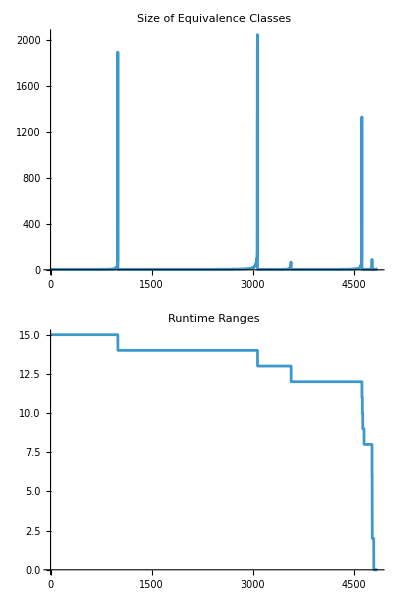

```mathematica
Column[
With[
{w=1600},
{
ListPlot[
Length/@haltgroupsSorted,
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Equivalence Classes"
],
ListPlot[
First/@haltgroupsSorted,
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Runtime Ranges"
]
}
]
]
```

## Existing Work

We will begin by recreating the results shown on page 761 of Stephen Wolfram’s A New Kind of Science. Wolfram found that the space of all 2-state 2-color Turing machines represents exactly 351 distinct functions.

We will first create a function that simulates the evolution of a Turing machine with a tape set to some  with rule  until it reaches a halt state. Wolfram set the halt state as when the head to move to the right of its starting position (where the digits are not defined). Clearly, not all Turing machines will halt, so we will need to set a maximum iteration count. Also, for now, only four bit numbers will be used, which can represent numbers from 0 to 15.

Initialize rules and max iteration count:

```mathematica
states=2;
colors=2;
maxiters=64;
rules=Range[0,(2*states*colors)^(states*colors)-1];
bits=4;
width=11;
```

Using a smaller width allows less buffer space for the Turing machine to move past our defined interval  to give it a chance to return to . Wolfram used a width of 11 in NKS and I will use the smallest width possible of bits, which if 4. This is why our results diverge slightly. Note that results will be the same for width  6.

```mathematica
Length[rules]
```

4096

Why 4096 rules? For a -state -color Turing machine, there are  possible transitions, and for each transition there are  states to move to,  colors to change to, and 2 directions to move in, which results in a total of  machines. For , we have . This is why a generalized solution is difficult. For each increase of , the number of Turing machines increases exponentially by a factor of itself: enumeration is .

We set the initial condition to start in state 1 at position 11 of a tape of length 11 containing the value .

Set the initial condition as a function of :

```mathematica
init[n_]:={{1,width},{IntegerDigits[n,2,width],0}}
```

The Block body loops through the Turing machine evolution and checks for termination, which is passed to a Transpose block that trims the tape to only contain the first 11 colors. Since it loops through each stage of a Turing machine, it runs in approximately maxiters^2 time.

Stepping through the Turing machine evolution at every step is slower than generating it all at once even though there’s more symbols generated on average???

```mathematica
trim[stages_List,width_Integer]:=
Module[
{min=Min[stages[[All,2]],stages[[1,2]]-width]-1,head,tail},
head=(#-{0,min,0})&/@stages[[All,1;;3]];
tail=ArrayPad[
stages[[All,4;;-1]],
{{0,0},{-min,stages[[1,2]]-(Length[stages[[1]]]-3)-stages[[1,3]]}}
];
Join[head[[#]],tail[[#]]]&/@Range[Length[head]]
]
```

SetDelayed::write: Tag CompiledFunction in CompiledFunction[{11,14.2,7646},{{_Integer,3},_Integer},«5»,Evaluate,LibraryFunction[/Users/msun/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/Michaels-MacBook-Pro-97912/compiledFunction2.dylib,compiledFunction2,{{Integer,3,Constant},{Integer,0,Constant}},{Integer,3}]][«1»] is Protected.

$Failed

Compiled function to include and trim states until halt:

```mathematica
cfindhalt=Compile[
{{evols,_Integer,2},{width,_Integer}},
Module[{min=Min[#[[All,2]],#[[1,2]]-width]-1,head,tail},
head=(#-{0,min,0})&/@#[[All,1;;3]];
tail=ArrayPad[
#[[All,4;;-1]],
{{0,0},{-min,#[[1,2]]-(Length[#[[1]]]-3)-#[[1,3]]}}
];
Join[head[[#]],tail[[#]]]&/@Range[Length[head]]
]&[
Module[{halt=False},
TakeWhile[
evols,
Which[
halt,
False,
(*1-width<=*)#[[3]]<=0,(* valid position *)
True,
MatchQ[#[[3]],1(*|-width*)],(* halt position *)
halt=True
]&
]
]
],
{{trim[_],_Integer,2}},
CompilationTarget->"C",
RuntimeAttributes->{Listable}
];
```

Compiled hist function:

```mathematica
chist[rule_Integer, num_Integer]:=
cfindhalt[
Flatten/@TuringMachine[{rule,states,colors},init[num],maxiters],width
]
```

Example for rule 2237 starting on a tape of all zeros ().

```mathematica
Grid[
{#[[1;;3]],#[[4;;-1]]}&/@chist[2237,3],
Alignment->Left
]
```

{1,12,0} | {0,0,0,0,0,0,0,0,0,0,1,1}
{2,11,-1} | {0,0,0,0,0,0,0,0,0,0,1,0}
{2,12,0} | {0,0,0,0,0,0,0,0,0,0,1,0}
{2,13,1} | {0,0,0,0,0,0,0,0,0,0,1,0}

Now that we can get the full evolution of a Turing machine, we want to see the final result on termination for each of these machines. The function is shown below, which loops through each rule, then each number constrained by bits bits, and returning the final tape.

Get the final stage of evolution for each rule and number:

```mathematica
getevols[rules_List,bits_Integer]:=
ParallelMap[
Join[{
#,
Table[
With[{h=chist[#,num]},
If[
h[[-1,3]]!=1,
-1,
FromDigits[h[[-1,4;;-1]],2]
]
],(* end With *)
{num,0,2^bits-1}
](* end Table over 2^bits-1 *)
}]&,(*end Join *)
rules
];(* end Table over r *)
```

Call the function:

```mathematica
evols=getevols[rules,bits];
%[[2238]] (* final state of rule 2237 *)
```

{2237,{-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14}}

The following two functions separate Turing machine equivalence classes into different groups.

Group rules by equivalence class and filter out non-terminating machines:

```mathematica
eqlgroups=
Map[
First,
GatherBy[
Select[
Transpose[{rules,evols}],
!ContainsOnly[#[[2,2]],{-1}]&
],
#[[2,2]]&
],
{2}
];
```

Number of groups:

```mathematica
Length[eqlgroups]
```

350

Group rules as above and additionally filter out unique machines:

```mathematica
multieqlgroups=
Map[
First,
Select[
GatherBy[
Select[
Transpose[{rules,evols}],
!ContainsOnly[#[[2,2]],{-1}]&
],
#[[2,2]]&
],
Length[#]>1&
],
{2}
];
```

For analysis purposes, multieqlgroups is more useful since we cannot say much about a Turing machine that is unique in what it does.

To measure the time complexity of each Turing machine, we are forced to do a brute-force simulation due to the Halting Problem.

Simulate the number of transitions until halt for all numbers of bits bits:

```mathematica
ht[rule_Integer,bits_Integer]:=
Select[
ParallelTable[
Module[{i=0,max=maxiters+1},(* 50 + 2n *)
NestWhile[
(i++;TuringMachine[{rule,states,colors},#])&,
{{1,width,0},{IntegerDigits[n,2,width],0}},
(*1-width<=*)#[[1,3]]<=0&,(* stop when dx > 0, or when x < 1 - width *)
1,max
];
If[i==max,-1,i]
],
{n,1,2^bits-1}
],
#!=-1&
]
```

Halting configuration for rule 2238 for all 4 bit numbers:

```mathematica
ht[2237,bits]
```

{3,5,3,7,3,5,3,9,3,5,3,7,3,5,3}

To analyze the time complexity difference between each group of Turing machines, it is helpful to have explicit access to those values.

Get the 3-tuples for each group of Turing machines {min,max,range}

```mathematica
halttimes=Map[{#,ht[#,bits]}&,eqlgroups,{2}];
```

```mathematica
((Max@@#[[2]])&/@#)&/@halttimes; 
MinMax/@%;
haltdifs=Append[#,#[[2]]-#[[1]]]&/@%;
```

Combine each group into {tuple,{rules...},{{runtimes}...}}:

```mathematica
haltcombined=Transpose@{haltdifs,eqlgroups,halttimes[[All,All,2]]};
```

THIS DOES NOTHING WTF Sort by largest range: corresponding slow and fast Turing machines:

```mathematica
sortedmachines={#[[1]],Transpose[#[[2;;3]]]}&/@SortBy[haltcombined,-#[[1,-1]]&];
```

```mathematica
list=Transpose@{sortedmachines[[All,1]],sortedmachines[[All,2,All,1]]};
```

List of the number of Turing machines in each  equivalence class:

```mathematica
Length@#[[2]]&/@list
```

{280,273,19,3,119,4,6,119,6,5,6,2,2,3,5,5,8,99,2,5,99,2,6,2,5,2,2,3,4,8,9,3,5,6,9,6,261,269,4,4,6,6,8,8,9,9,11,11,12,12,14,14,19,19,3,2,2,4,4,4,17,2,3,4,4,4,17,226,226,232,232,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,8,8,11,11,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,3,3,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,3,3,8,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

### POTENTIALLY OUTDATED SECTION

The number of unique functions 351 we found here is the same number Wolfram found in NKS (Wolfram, 759).

Find the last group (it turns out) of size 17 and see the outputs:

```mathematica
Length@#[[2]]&/@list;
Position[%,17,-1][[2,1]];
If[%!=-1,evols[[list[[%,2,1]]+1,2]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

## Distribution Analysis

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First@index,#}&/@value]]@l
```

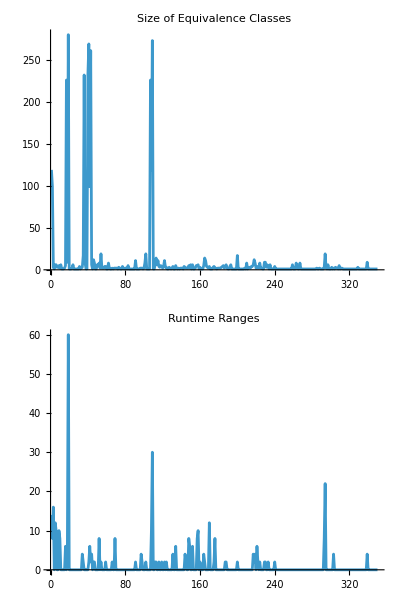

```mathematica
Column[
With[
{w=1600},
{
ListPlot[
Length/@eqlgroups,
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Equivalence Classes"
],
ListPlot[
haltdifs[[All,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Runtime Ranges"
]
}
]
]
```

Generally, spikes in the size of equivalence classes, aside from the first, generally corresponds to spikes in runtime range, yet there are also some spikes where there is low runtime range.
Spikes in runtime ranges are more frequent. Some spikes correspond with large equivalence classes, but there is a spike at group 295 where the size is very small. Large runtime ranges also happen during the large size spike in the beginning.

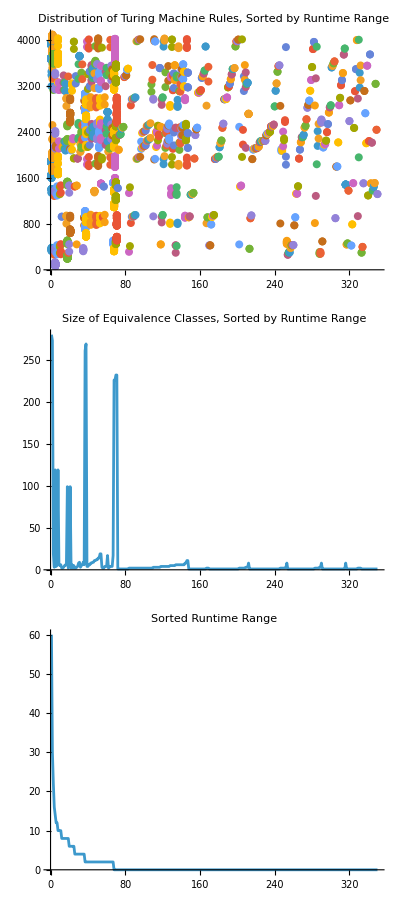

```mathematica
Column[
With[{w=1600},
{
ListPlot[
stackPoints[list[[All,2]]],
PlotRange->Full,
ImageSize->{w,Automatic},
AspectRatio->1/3,
PlotLabel->"Distribution of Turing Machine Rules, Sorted by Runtime Range"
],
ListPlot[
Length/@list[[All,2]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Size of Equivalence Classes, Sorted by Runtime Range"
],
ListPlot[
list[[All,1,3]],
PlotRange->All,
Joined->True,
ImageSize->{w,Automatic},
AspectRatio->1/8,
PlotLabel->"Sorted Runtime Range"
]
}
]
]
```

larger groups of isomorphic rules generally correspond to a larger difference so we only pick the large groups??

## Future Directions

stream algorithm?
analyze state diagram patterns to extend beyond dfa minimzation
optimize htdp for parallel cores by sacrificing total dp?? test performance
make dp better by extrapolating directions/skip steps